# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Append[makeColors[6],Gray]
```

{RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],RGBColor[0.4305106, 0.702073568, 0.5395238880000001],RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],RGBColor[0.897113792, 0.5919722799999999, 0.218624288],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
colorRamp[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

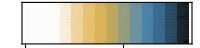

```mathematica
gaPanel=Rotate[DensityPlot[(x-0.5)/2,{x,0,2.5},{y,0,1},ColorFunction->colorRamp,ColorFunctionScaling->False,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200],Pi/2]
```

## Immune escape

```mathematica
escape=Import["../escape-score/escape_scores.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding
AY.1 | recombinant | XBA | XBA | 0.193466 | -3.41014
AY.10 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.100 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.101 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.102 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.102.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.102.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.103 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.103.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.103.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.104 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.106 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.105 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.107 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.109 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.108 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.11 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.110 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.112 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.111 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.112.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.112.2 | recombinant | XBA | XBA | 0.328761 | -2.91616
AY.113 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.112.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.114 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.116 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.117 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.116.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.118 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.119 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.119.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.119.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.120 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.120.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.121 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.120.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.120.2.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.121.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122.2 | recombinant | XBA | XBA | 0.194869 | -3.19149
AY.122.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122.5 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.123 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.122.6 | recombinant | XBA | XBA | 0.193466 | -2.92333
AY.123.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.124 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.124.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.124.1.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.125 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.125.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.127 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.126 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.127.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.127.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.128 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.127.3 | recombinant | XBA | XBA | 0.310807 | -3.1833
AY.129 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.13 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.131 | recombinant | XBA | XBA | 0.326757 | -1.64976
AY.132 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.133 | recombinant | XBC | XBC | 0.272276 | -3.5153
AY.134 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.14 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.15 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.16 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.16.1 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.17 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.18 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.19 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.2 | recombinant | XBC | XBC | 0.193466 | -3.41014
AY.20 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.20.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.21 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.22 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.23 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.23.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.23.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.24 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.24.1 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.25 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.25.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.25.1.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.25.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.25.1.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.25.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.26 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.27 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.26.1 | recombinant | XBC | XBC | 0.328761 | -2.91616
AY.28 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.29 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.29.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.29.2 | recombinant | XBA | XBA | 0.194214 | -2.74827
AY.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.3.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.3.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.3.3 | recombinant | XBA | XBA | 0.194214 | -2.74827
AY.3.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.30 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.32 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.31 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.33 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.33.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.33.2 | recombinant | XBA | XBA | 0.371125 | -2.60216
AY.34 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.34.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.34.1.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.35 | recombinant | XBA | XBA | 0.328761 | -2.91616
AY.34.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.36 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.36.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.37 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.38 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.39 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.1.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.1.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.1.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.1.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.39.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.1 | recombinant | XBA | XBA | 0.310807 | -3.11784
AY.4.10 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.11 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.12 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.13 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.14 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.15 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.17 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.16 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.2.5 | recombinant | XBA | XBA | 0.194214 | -2.68528
AY.4.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.5 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.6 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.9 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.7 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.4.8 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.40 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.41 | recombinant | XBA | XBA | 0.197877 | -2.75838
AY.42 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.42.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.5 | recombinant | XBA | XBA | 0.210858 | -2.53649
AY.43.6 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.7 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.8 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.44 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.43.9 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.45 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.5 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.6 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.46.6.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.47 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.48 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.49 | recombinant | XBC | XBC | 0.193466 | -4.01472
AY.5 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.3 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.4 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.5 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.6 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.5.7 | recombinant | XBA | XBA | 0.193466 | 0.38716
AY.50 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.51 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.52 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.54 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.53 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.55 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.56 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.57 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.59 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.58 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.6 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.60 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.61 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.62 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.63 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.64 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.66 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.65 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.67 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.68 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.7 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.69 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.7.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.7.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.71 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.72 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.70 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.73 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.74 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.75.2 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.75 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.75.3 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.77 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.76 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.78 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.79 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.8 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.80 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.81 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.82 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.83 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.84 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.85 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.86 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.87 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.88 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.9 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.9.2 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.9.2.1 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.9.2.2 | recombinant | XBC | XBC | 0.193466 | -2.65447
AY.90 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.91 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.92 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.91.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.93 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.94 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.95 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.98 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.98.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.98.1.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.99 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.99.1 | recombinant | XBA | XBA | 0.193466 | -2.65447
AY.99.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
B.1.617.2 | recombinant | XBA | XBA | 0.193466 | -2.65447
BA.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.1 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.1 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.10 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.11 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.12 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.13 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.14 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.15 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.16 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.17 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.18 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.2 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.3 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.4 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.5 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.6 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.7 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.9 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.1.8 | recombinant | XP | XP | 0.35873 | 0.0232
BA.1.12 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.10 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.13 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.13.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.14 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.14.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.15 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.14.2 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.15.2 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.15.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.15.3 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.16 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.16.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.16.2 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.17 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.17.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.18 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.17.2 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.2 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.19 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.20 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.21 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.21.1 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.22 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.24 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.23 | recombinant | XP | XP | 0.534676 | -0.90204
BA.1.4 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.3 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.6 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.8 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.5 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.7 | recombinant | XP | XP | 0.152758 | -0.02911
BA.1.9 | recombinant | XP | XP | 0.152758 | -0.02911
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.000089996 | 0
BA.2 | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.000089996 | 0
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.000089996 | 0
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.000089996 | 0
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.000089996 | 0
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.000089996 | 0
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.000089996 | 0
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.000089996 | 0
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.000089996 | 0
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.000089996 | 0
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.000089996 | 0
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.000089996 | 0
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.000089996 | 0
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.000089996 | 0
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.000089996 | 0
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.000089996 | 0
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.000089996 | 0
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.000089996 | 0
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.000089996 | 0
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.000089996 | 0
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.000089996 | 0
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.000089996 | 0
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.000089996 | 0
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.000089996 | 0
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.000089996 | 0
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.000089996 | 0
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.000089996 | 0
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.000089996 | 0
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.000089996 | 0
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.000089996 | 0
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.000089996 | 0
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.000089996 | 0
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.000089996 | 0
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.000089996 | 0
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.000089996 | 0
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.000089996 | 0
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.000089996 | 0
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.000089996 | 0
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.000089996 | 0
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.000089996 | 0
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.000089996 | 0
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.000089996 | 0
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.000089996 | 0
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.000089996 | 0
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.000089996 | 0
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.000089996 | 0
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.000089996 | 0
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.000089996 | 0
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.000089996 | 0
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.000089996 | 0
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.000089996 | 0
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.000089996 | 0
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.000089996 | 0
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.000089996 | 0
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.000089996 | 0
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.000089996 | 0
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.000089996 | 0
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.000089996 | 0
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.000089996 | 0
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.000089996 | 0
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.000089996 | 0
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.000089996 | 0
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.000089996 | 0
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.000089996 | 0
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.000089996 | 0
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.000089996 | 0
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.000089996 | 0
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.000089996 | 0
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.000089996 | 0
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.000089996 | 0
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.000089996 | 0
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.000089996 | 0
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.000089996 | 0
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.000089996 | 0
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.000089996 | 0
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.000089996 | 0
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.000089996 | 0
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.000089996 | 0
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.000089996 | 0
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.000089996 | 0
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.000089996 | 0
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.000089996 | 0
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.162048 | 0.13507
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.000089996 | 0
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.000089996 | 0
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.000089996 | 0
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138
BA.4.8 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.46306
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875
BA.5.2.15 | 22B (Omicron) | CF.1 | BA.5.2.27.1 | 0.386325 | 0.55831
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831
BC.1 | recombinant | XP | XP | 0.35873 | 0.0232
BD.1 | recombinant | XP | XP | 0.152758 | -0.02911
BC.2 | recombinant | XP | XP | 0.35873 | 0.0232
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.22218
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569
BQ.1 | 22E (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401
BQ.1.1 | 22E (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831
XAA | recombinant | XAA | XAA | -0.000089996 | 0
XAB | recombinant | XAB | XAB | -0.000089996 | 0
XAC | recombinant | XAC | XAC | -0.000089996 | 0
XAD | recombinant | XAD | XAD | -0.000089996 | 0
XAE | recombinant | XAE | XAE | -0.000089996 | -0.26796
XAF | recombinant | XAF | XAF | -0.000089996 | 0
XAG | recombinant | XAG | XAG | -0.000089996 | -0.28094
XAH | recombinant | XAH | XAH | -0.000089996 | 0
XAJ | recombinant | XAJ | XAJ | 0.386325 | 0.35483
XAK | recombinant | XAK | XAK | 0.276938 | 1.15166
XAL | recombinant | XAL | XAL | -0.000089996 | 0
XAM | recombinant | XAM | XAM | -0.000089996 | 0.75567
XAN | recombinant | XAN | XAN | 0.386325 | 0.55831
XAP | recombinant | XAP | XAP | -0.000089996 | 0
XAQ | recombinant | XAQ | XAQ | -0.000089996 | 0
XAR | recombinant | XAR | XAR | -0.000089996 | 0
XAS | recombinant | XAS | XAS | 0.386325 | 0.55831
XAT | recombinant | XAT | XAT | -0.000089996 | 0
XAU | recombinant | XAU | XAU | -0.000089996 | 0
XAV | recombinant | XAV | XAV | 0.386325 | 0.55831
XAW | recombinant | XAW | XAW | 0.212 | 0.91409
XAY | recombinant | XAY | XAY | 0.528346 | 0.72704
XAZ | recombinant | XAZ | XAZ | 0.386325 | 0.55831
XBA | recombinant | XBA | XBA | 0.315502 | 0.20216
XBB | recombinant | XBB | XBB | 0.907001 | 0.40687
XC | recombinant | XBA | XBA | 0.193466 | -2.65447
XD | recombinant | XBA | XBA | 0.152758 | -0.02911
XE | recombinant | XE | XE | -0.000089996 | 0
XG | recombinant | XG | XG | -0.000089996 | 0
XF | recombinant | XP | XP | 0.152758 | -0.02911
XH | recombinant | XH | XH | -0.000089996 | 0
XJ | recombinant | XJ | XJ | -0.000089996 | 0
XK | recombinant | XK | XK | -0.000089996 | -3.62446
XM | recombinant | XM | XM | -0.000089996 | 0
XL | recombinant | XL | XL | -0.000089996 | 0
XN | recombinant | XN | XN | -0.000089996 | 0
XR | recombinant | XR | XR | -0.000089996 | 0
XQ | recombinant | XQ | XQ | -0.000089996 | 0
XP | recombinant | XP | XP | 0.35873 | 0.0232
XS | recombinant | XP | XP | -0.000089996 | 0
XV | recombinant | XV | XV | -0.000089996 | -0.17271
XT | recombinant | XT | XT | -0.000089996 | -0.17271
XU | recombinant | XU | XU | -0.000089996 | -0.09525
XW | recombinant | XW | XW | -0.000089996 | 0
XY | recombinant | XY | XY | -0.000089996 | 0
XZ | recombinant | XZ | XZ | -0.000089996 | 0

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],"22E (Omicron)"->colors[[5]],"22F (Omicron)"->colors[[6]],_->colors[[7]] }
```

{21L (Omicron)→RGBColor[0.30382016, 0.13051672, 0.67703096],22A (Omicron)→RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],22B (Omicron)→RGBColor[0.4305106, 0.702073568, 0.5395238880000001],22D (Omicron)→RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],22E (Omicron)→RGBColor[0.897113792, 0.5919722799999999, 0.218624288],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.60014 | 1.60942 | 1.59201
USA | BA.1 | 0.647013 | 0.651587 | 0.642068
USA | BA.1.1 | 0.676453 | 0.677796 | 0.675216
USA | BA.1.1.1 | 0.675129 | 0.689134 | 0.658139
USA | BA.1.1.10 | 0.75963 | 0.769792 | 0.74802
USA | BA.1.1.14 | 0.680946 | 0.696376 | 0.661834
USA | BA.1.1.16 | 0.737527 | 0.753851 | 0.720137
USA | BA.1.1.18 | 0.639592 | 0.644385 | 0.634317
USA | BA.1.1.2 | 0.613078 | 0.628886 | 0.591904
USA | BA.1.15 | 0.628774 | 0.633617 | 0.622504
USA | BA.1.15.2 | 0.673764 | 0.69339 | 0.661282
USA | BA.1.17.2 | 0.68198 | 0.697232 | 0.667453
USA | BA.1.18 | 0.673288 | 0.685969 | 0.659818
USA | BA.1.20 | 0.675149 | 0.682803 | 0.664459
USA | BA.2.1 | 1.03659 | 1.041 | 1.03237
USA | BA.2.10 | 0.882551 | 0.884587 | 0.880109
USA | BA.2.10.1 | 0.906984 | 0.913688 | 0.900966
USA | BA.2.12 | 1.20975 | 1.21406 | 1.20458
USA | BA.2.12.1 | 1.22185 | 1.22241 | 1.22133
USA | BA.2.13 | 1.22452 | 1.22748 | 1.22023
USA | BA.2.13.1 | 1.35992 | 1.365 | 1.35353
USA | BA.2.16 | 0.973913 | 0.985643 | 0.959678
USA | BA.2.18 | 1.21919 | 1.22155 | 1.21677
USA | BA.2.20 | 1.04371 | 1.04921 | 1.03667
USA | BA.2.21 | 0.996386 | 1.00196 | 0.991415
USA | BA.2.22 | 1.05795 | 1.06494 | 1.0488
USA | BA.2.23 | 1.10098 | 1.10561 | 1.09607
USA | BA.2.23.1 | 1.06114 | 1.06878 | 1.05315
USA | BA.2.26 | 0.931141 | 0.936325 | 0.926955
USA | BA.2.3 | 0.997662 | 0.998789 | 0.996437
USA | BA.2.3.10 | 0.998778 | 1.01024 | 0.990099
USA | BA.2.3.14 | 1.01005 | 1.02282 | 0.996199
USA | BA.2.3.17 | 0.975182 | 0.980365 | 0.970109
USA | BA.2.3.2 | 1.11347 | 1.12249 | 1.10406
USA | BA.2.3.4 | 0.981768 | 0.990476 | 0.975447
USA | BA.2.3.6 | 1.0684 | 1.07595 | 1.05908
USA | BA.2.31 | 1.03089 | 1.03668 | 1.02348
USA | BA.2.32 | 0.968447 | 0.97749 | 0.95926
USA | BA.2.36 | 1.17503 | 1.18029 | 1.16959
USA | BA.2.37 | 1.00488 | 1.00959 | 1.0007
USA | BA.2.38 | 1.35864 | 1.36291 | 1.35279
USA | BA.2.40.1 | 1.19414 | 1.20116 | 1.18706
USA | BA.2.41 | 1.17887 | 1.18682 | 1.17185
USA | BA.2.47 | 1.10107 | 1.10968 | 1.09219
USA | BA.2.48 | 1.17274 | 1.17584 | 1.16932
USA | BA.2.5 | 0.976633 | 0.991815 | 0.963815
USA | BA.2.52 | 1.27806 | 1.28754 | 1.26781
USA | BA.2.56 | 1.30506 | 1.30943 | 1.30006
USA | BA.2.59 | 1.11208 | 1.11799 | 1.10626
USA | BA.2.6 | 1.01784 | 1.026 | 1.01112
USA | BA.2.65 | 1.08835 | 1.09168 | 1.08608
USA | BA.2.7 | 0.923216 | 0.925586 | 0.920273
USA | BA.2.72 | 1.12505 | 1.13144 | 1.12037
USA | BA.2.73 | 1.02089 | 1.02643 | 1.01553
USA | BA.2.75 | 2.05361 | 2.0574 | 2.04966
USA | BA.2.75.1 | 2.09101 | 2.09543 | 2.08626
USA | BA.2.75.2 | 2.21011 | 2.21417 | 2.20558
USA | BA.2.75.3 | 2.32112 | 2.32945 | 2.31423
USA | BA.2.76 | 1.58412 | 1.58797 | 1.57989
USA | BA.2.8 | 1.04531 | 1.05784 | 1.03525
USA | BA.2.9 | 1.01842 | 1.01922 | 1.01759
USA | BA.2.9.2 | 0.815868 | 0.822738 | 0.808561
USA | BA.2.9.3 | 1.2247 | 1.23509 | 1.21724
USA | BA.4 | 1.58638 | 1.5872 | 1.58554
USA | BA.4.1 | 1.55801 | 1.55859 | 1.55725
USA | BA.4.1.1 | 1.55136 | 1.55354 | 1.54905
USA | BA.4.1.6 | 1.5394 | 1.54267 | 1.53753
USA | BA.4.1.8 | 1.91377 | 1.91666 | 1.91104
USA | BA.4.1.9 | 2.03005 | 2.03797 | 2.02437
USA | BA.4.2 | 1.58003 | 1.58141 | 1.57883
USA | BA.4.3 | 1.59109 | 1.59456 | 1.58795
USA | BA.4.4 | 1.5822 | 1.58321 | 1.58102
USA | BA.4.6 | 1.9455 | 1.94617 | 1.94484
USA | BA.5 | 1.78892 | 1.7897 | 1.78798
USA | BA.5.1 | 1.80766 | 1.80817 | 1.80696
USA | BA.5.1.1 | 1.73296 | 1.73369 | 1.73228
USA | BA.5.1.10 | 1.85678 | 1.85781 | 1.85586
USA | BA.5.1.12 | 2.05535 | 2.05969 | 2.05051
USA | BA.5.1.18 | 2.07612 | 2.07926 | 2.07268
USA | BA.5.1.2 | 1.88779 | 1.88988 | 1.88586
USA | BA.5.1.21 | 1.86928 | 1.87402 | 1.8633
USA | BA.5.1.22 | 1.8411 | 1.8422 | 1.83965
USA | BA.5.1.23 | 1.83269 | 1.83385 | 1.83108
USA | BA.5.1.24 | 1.82647 | 1.82816 | 1.82398
USA | BA.5.1.25 | 1.80258 | 1.80401 | 1.80101
USA | BA.5.1.27 | 2.1978 | 2.20271 | 2.19193
USA | BA.5.1.3 | 1.81919 | 1.8211 | 1.81754
USA | BA.5.1.5 | 2.05634 | 2.05901 | 2.05377
USA | BA.5.1.6 | 1.87886 | 1.88067 | 1.87717
USA | BA.5.1.7 | 1.96029 | 1.96323 | 1.9563
USA | BA.5.1.8 | 1.75452 | 1.75799 | 1.75131
USA | BA.5.10.1 | 2.06606 | 2.0694 | 2.06131
USA | BA.5.2 | 1.8888 | 1.88932 | 1.88808
USA | BA.5.2.1 | 1.81584 | 1.81638 | 1.8152
USA | BA.5.2.16 | 1.95467 | 1.95967 | 1.94925
USA | BA.5.2.19 | 1.99044 | 1.99443 | 1.98574
USA | BA.5.2.2 | 1.75495 | 1.75954 | 1.75027
USA | BA.5.2.20 | 1.90578 | 1.90688 | 1.90467
USA | BA.5.2.21 | 1.87668 | 1.87758 | 1.87574
USA | BA.5.2.22 | 2.00042 | 2.00283 | 1.99828
USA | BA.5.2.23 | 2.2801 | 2.2877 | 2.27068
USA | BA.5.2.27 | 1.89612 | 1.89861 | 1.89329
USA | BA.5.2.28 | 1.93447 | 1.9369 | 1.93181
USA | BA.5.2.3 | 1.9122 | 1.91395 | 1.91012
USA | BA.5.2.31 | 1.93727 | 1.93909 | 1.93461
USA | BA.5.2.33 | 1.90937 | 1.91478 | 1.90484
USA | BA.5.2.34 | 2.43626 | 2.44011 | 2.431
USA | BA.5.2.6 | 2.09363 | 2.09772 | 2.08933
USA | BA.5.2.8 | 1.90643 | 1.91169 | 1.90115
USA | BA.5.2.9 | 1.87962 | 1.88046 | 1.87852
USA | BA.5.3 | 1.60714 | 1.60891 | 1.6051
USA | BA.5.3.1 | 1.73547 | 1.73771 | 1.73333
USA | BA.5.5 | 1.6439 | 1.64443 | 1.64341
USA | BA.5.5.1 | 1.95243 | 1.95387 | 1.95102
USA | BA.5.5.2 | 1.75965 | 1.76214 | 1.75685
USA | BA.5.5.3 | 1.77286 | 1.77636 | 1.76936
USA | BA.5.6 | 1.74205 | 1.74251 | 1.74137
USA | BA.5.6.2 | 1.89792 | 1.9011 | 1.89582
USA | BA.5.8 | 1.71396 | 1.71556 | 1.71231
USA | BA.5.9 | 2.08333 | 2.08816 | 2.07946
USA | BE.1 | 1.75711 | 1.75821 | 1.75621
USA | BE.1.1 | 1.82601 | 1.82714 | 1.82517
USA | BE.1.1.1 | 2.07607 | 2.08055 | 2.07271
USA | BE.1.1.2 | 2.00299 | 2.00847 | 1.99674
USA | BE.1.2 | 2.03378 | 2.03783 | 2.02978
USA | BE.1.4 | 1.79627 | 1.79823 | 1.79438
USA | BE.1.4.1 | 1.80357 | 1.81075 | 1.79777
USA | BE.2 | 1.83265 | 1.8349 | 1.83009
USA | BE.3 | 1.71408 | 1.715 | 1.71318
USA | BE.4 | 1.8964 | 1.90034 | 1.89337
USA | BE.5 | 1.64107 | 1.64614 | 1.63623
USA | BF.1 | 1.67679 | 1.67833 | 1.67542
USA | BF.1.1 | 1.38659 | 1.39077 | 1.38152
USA | BF.10 | 1.82806 | 1.82887 | 1.82713
USA | BF.11 | 2.1753 | 2.1773 | 2.17361
USA | BF.13 | 1.97334 | 1.97518 | 1.97135
USA | BF.14 | 1.99087 | 2.00008 | 1.9835
USA | BF.16 | 1.92311 | 1.92765 | 1.91874
USA | BF.21 | 1.75531 | 1.75654 | 1.75395
USA | BF.24 | 1.76675 | 1.76791 | 1.76552
USA | BF.25 | 2.05887 | 2.06297 | 2.05453
USA | BF.26 | 1.88601 | 1.88717 | 1.88495
USA | BF.27 | 1.77195 | 1.77325 | 1.77076
USA | BF.28 | 1.70157 | 1.70291 | 1.70023
USA | BF.3 | 1.89343 | 1.89674 | 1.88988
USA | BF.4 | 1.79305 | 1.79532 | 1.79071
USA | BF.5 | 1.90992 | 1.91103 | 1.90904
USA | BF.7 | 2.24861 | 2.25029 | 2.24743
USA | BF.7.4 | 2.27924 | 2.28142 | 2.27569
USA | BF.8 | 1.73098 | 1.73195 | 1.72982
USA | BF.9 | 1.80274 | 1.8041 | 1.8014
USA | BG.2 | 1.26747 | 1.26822 | 1.26684
USA | BG.4 | 1.22996 | 1.23487 | 1.22474
USA | BG.5 | 1.30706 | 1.30882 | 1.30512
USA | BK.1 | 1.866 | 1.86767 | 1.86487
USA | BQ.1 | 2.75834 | 2.76027 | 2.75554
USA | BQ.1.1 | 2.83826 | 2.84047 | 2.83416
USA | BU.2 | 1.92238 | 1.92911 | 1.91464
USA | XAP | 1.11581 | 1.12097 | 1.10903
USA | XAS | 1.80419 | 1.80881 | 1.80038
USA | XE | 1.0671 | 1.07303 | 1.06133
USA | XZ | 1.10756 | 1.11585 | 1.09908
USA | other | 1.53204 | 1.5326 | 1.53157

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.1,BA.1.1,BA.1.1.1,BA.1.1.10,BA.1.1.14,BA.1.1.16,BA.1.1.18,BA.1.1.2,BA.1.15,BA.1.15.2,BA.1.17.2,BA.1.18,BA.1.20,BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.1,BA.2.75.2,BA.2.75.3,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.1.9,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.21,BA.5.1.3,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.1.8,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.23,BA.5.2.3,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.2,BE.3,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.14,BF.16,BF.21,BF.24,BF.3,BF.4,BF.5,BF.7,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,BQ.1,BQ.1.1,XAP,XAS,XE,XZ}

```mathematica
Length[pangoLineages]
```

140

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.775215

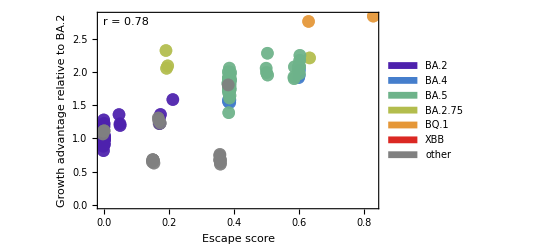

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.877167

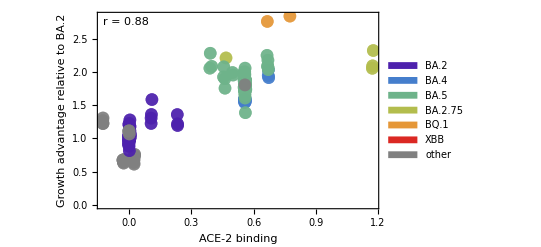

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.005]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.005]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.754069

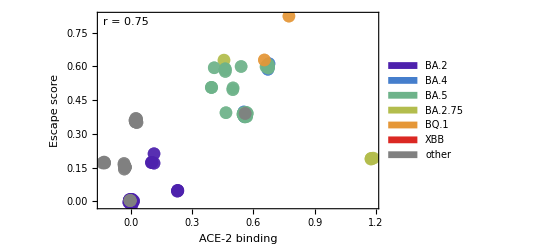

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_escape_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation.png

```mathematica
gaColors=Table[colorRamp[((pangoLineage/.pangoGAMapping)-0.5)/2],{pangoLineage,pangoLineages}]
```

{RGBColor[0.95829255765216, 0.90728891768628, 0.79238789767152],RGBColor[0.9519428992848, 0.8907253894734, 0.7528145594856],RGBColor[0.95222839278288, 0.8914701192425399, 0.75459385690536],RGBColor[0.93400343857584, 0.8439290507752201, 0.6410094347944801],RGBColor[0.95097387780144, 0.88819762912002, 0.7467752715976801],RGBColor[0.9387705027636, 0.85636427131755, 0.6707194809642001],RGBColor[0.95989310705856, 0.9114640628224799, 0.80236309307232],RGBColor[0.965611504944096, 0.926380903891668, 0.8380021905345121],RGBColor[0.96222614344704, 0.91754995151232, 0.8169034088908801],RGBColor[0.95252294477376, 0.89223847872408, 0.75642961008672],RGBColor[0.950750844768, 0.887615831844, 0.745385250096],RGBColor[0.95262549985296, 0.8925060008251801, 0.7570687699591201],RGBColor[0.9522242517576, 0.8914593170883, 0.7545680485571999],RGBColor[0.8889780566089599, 0.7321988497106799, 0.3790065912411199],RGBColor[0.911053679436988, 0.7854484777222915, 0.502485030293186],RGBColor[0.90755211753592, 0.77700219875911, 0.48289929080324],RGBColor[0.8329008952999998, 0.6783100058375, 0.3031273978500001],RGBColor[0.8223898744894399, 0.67580479061402, 0.31109909953368],RGBColor[0.8200660637249598, 0.6752509294611799, 0.31286150934312007],RGBColor[0.70241888611808, 0.64721069382164, 0.40208673500976],RGBColor[0.89796036191632, 0.75386548263106, 0.42924848235703994],RGBColor[0.82469422168784, 0.67635401278622, 0.30935145115847995],RGBColor[0.8879573140399599, 0.7297366694805549, 0.37329713968561995],RGBColor[0.8947396880198799, 0.746096746579165, 0.4112338701068601],RGBColor[0.8859171187135599, 0.7248154202343551, 0.36188545104482006],RGBColor[0.8797497698982399, 0.70993887370192, 0.32738882049728],RGBColor[0.88546015279492, 0.723713151665485, 0.35932944441373993],RGBColor[0.9040901485516, 0.76865142369655, 0.46353501150020004],RGBColor[0.89455680706624, 0.74565561099592, 0.41021093839328004],RGBColor[0.8897951952512799, 0.73416990751849, 0.38357719859516004],RGBColor[0.89439688475908, 0.745269855022765, 0.40931642424925996],RGBColor[0.89278198331092, 0.741374476755985, 0.40028358691574],RGBColor[0.8977785414744399, 0.7534269051571449, 0.42823148254117993],RGBColor[0.87795958305364, 0.705620681445745, 0.31737553666358],RGBColor[0.89874375765406, 0.7557551476224175, 0.43363035115457005],RGBColor[0.8968347376005039, 0.751150312302007, 0.422952382149188],RGBColor[0.8844188305652799, 0.7212013302867399, 0.3535048819781599],RGBColor[0.8630655126325999, 0.685499493891425, 0.28025014024469996],RGBColor[0.89352292275016, 0.74316173095153, 0.40442797940251995],RGBColor[0.7035253550933599, 0.6474744115871299, 0.4012475738329201],RGBColor[0.8464636990027999, 0.68154258837365, 0.29284118235659995],RGBColor[0.8597363739237199, 0.684706021104635, 0.28277500449233994],RGBColor[0.8797374307006, 0.709909109754175, 0.3273198020657],RGBColor[0.8650607019376398, 0.685975030826495, 0.27873696143658],RGBColor[0.8975705521883199, 0.75292520460706, 0.42706810914104],RGBColor[0.77354544717524, 0.664163123729795, 0.34814338005378],RGBColor[0.7500862890299599, 0.658571826635555, 0.36593512586562005],RGBColor[0.8781593892017199, 0.706102643071135, 0.31849313825833997],RGBColor[0.8916656657023599, 0.738681755564755, 0.39403954311841993],RGBColor[0.88155967652908, 0.714304632964015, 0.3375124055642599],RGBColor[0.9052258993216, 0.7713910205128, 0.4698877533152],RGBColor[0.8763006417049599, 0.7016190725036799, 0.3080963652531199],RGBColor[0.8912287061947599, 0.7376277453827049, 0.3915954409362199],RGBColor[0.2141467079937801, 0.4066412544740401, 0.5406418179372302],RGBColor[0.2024445830714601, 0.38442019488828005, 0.5110982487131103],RGBColor[0.16199307195557605, 0.30174979095156806, 0.3990381528073162],RGBColor[0.11910769189006398, 0.20534752893795194, 0.26538136869442397],RGBColor[0.50558887133834, 0.5978355875481199, 0.5499757417611901],RGBColor[0.8877286591057599, 0.7291851203675801, 0.37201817444072005],RGBColor[0.89158185661084, 0.738479595789595, 0.39357076287698],RGBColor[0.9218740951488, 0.8122888096104, 0.5654150355936001],RGBColor[0.8199069664504399, 0.675213009936395, 0.31298217088818],RGBColor[0.503567668627436, 0.5972875914470479, 0.5514712570318261],RGBColor[0.5289029749352541, 0.604156595234372, 0.532725320632089],RGBColor[0.5348361281660119, 0.605765214112616, 0.528335300169642],RGBColor[0.5455151253658699, 0.60866054410466, 0.5204337654540451],RGBColor[0.25789536669338603, 0.489715188329148, 0.6510911196951512],RGBColor[0.221517820293128, 0.4206381932099039, 0.559251170334348],RGBColor[0.509238126224006, 0.598824987294308, 0.547275608628321],RGBColor[0.49936203831803594, 0.596147345097848, 0.5545830598789261],RGBColor[0.50730148257686, 0.5982999171654799, 0.5487085575020101],RGBColor[0.24796817667968005, 0.47086453665024003, 0.6260286094828802],RGBColor[0.3227206542899659, 0.548255666933588, 0.6852824131971812],RGBColor[0.3059833171567219, 0.543717776972396, 0.6976665957126272],RGBColor[0.21025235069521409, 0.3992462944856521, 0.5308099954949492],RGBColor[0.37268657827711393, 0.561802616669852, 0.6483119490615992],RGBColor[0.27572662189396996, 0.5235747981804598, 0.6961084926823949],RGBColor[0.21360296151974006, 0.4056087391933201, 0.5392690577160902],RGBColor[0.207103407866756, 0.3932667953188079, 0.522860070925446],RGBColor[0.26602594076818403, 0.505154262188112, 0.6716178342538441],RGBColor[0.27181421271303796, 0.5161455596352839, 0.686231095864533],RGBColor[0.29568889850766195, 0.540926715367316, 0.7052835755479172],RGBColor[0.21329251294310608, 0.405019231188108, 0.5384852890351712],RGBColor[0.268818476241506, 0.5104569826393079, 0.6786679610995711],RGBColor[0.243343390789088, 0.46208257238918393, 0.6143527230082081],RGBColor[0.3534325598217799, 0.5565823945780399, 0.6625582581852302],RGBColor[0.265708108752662, 0.504550733837316, 0.670815425100417],RGBColor[0.29868489667690395, 0.541739001689072, 0.7030667959103643],RGBColor[0.24510077438746397, 0.4654196522711519, 0.618789471405324],RGBColor[0.23391001517965404, 0.444169620433572, 0.5905369128724891],RGBColor[0.35305441025998996, 0.55647986924282, 0.6628380561694651],RGBColor[0.260394629471216, 0.494461015901088, 0.6574008406540561],RGBColor[0.26949966105044, 0.5117504783359199, 0.6803877026585401],RGBColor[0.230786601529724, 0.43823859839383195, 0.582651440106234],RGBColor[0.13495325297381602, 0.24096684556788803, 0.31476572144315607],RGBColor[0.258387679381274, 0.490650036456732, 0.6523340284891591],RGBColor[0.201625584498536, 0.3828650058768479, 0.509030577995676],RGBColor[0.26019246090302, 0.49407711982835995, 0.6568904392415701],RGBColor[0.268579046335532, 0.5100023313479759, 0.678063488488962],RGBColor[0.4850305717380079, 0.592261743833744, 0.5651871061754281],RGBColor[0.3704486650617319, 0.561195865199576, 0.6499678113706622],RGBColor[0.45220835056431796, 0.583362859454324, 0.5894727123230131],RGBColor[0.24580148150939, 0.46675021871201994, 0.6205584996373651],RGBColor[0.348852887360234, 0.555340736510012, 0.6659468198885191],RGBColor[0.33705676402872203, 0.552142527068396, 0.6746749313646271],RGBColor[0.36456658657698193, 0.559601093899076, 0.6543200409365372],RGBColor[0.262856192910656, 0.499135256539008, 0.6636153846240961],RGBColor[0.3896541089334499, 0.5664029175670999, 0.6357574432395752],RGBColor[0.204849707003468, 0.38898726305402387, 0.517170303647538],RGBColor[0.3511248206424499, 0.5559567116291, 0.6642657856710752],RGBColor[0.2895991279613479, 0.5392756338118639, 0.7097894792841182],RGBColor[0.2071196138894, 0.3932975687891999, 0.5229009851829001],RGBColor[0.220348827945458, 0.41841840417284387, 0.556299893829003],RGBColor[0.28366856418449593, 0.5376677169961279, 0.7141775837745362],RGBColor[0.38954695911665005, 0.5663738667047, 0.635836724840775],RGBColor[0.42284197885697006, 0.57540093801446, 0.611201288627895],RGBColor[0.287773741540646, 0.538780728161828, 0.7111401074285612],RGBColor[0.6792411676626798, 0.641686475559065, 0.41966503311846004],RGBColor[0.17543892250687998, 0.3319747861798399, 0.44094355603807994],RGBColor[0.23925916022522, 0.45432706376795995, 0.60404154027927],RGBColor[0.23377367184628997, 0.4439107193062199, 0.590192696011515],RGBColor[0.254974747326812, 0.484169250527016, 0.6437176280424421],RGBColor[0.352732871518076, 0.556392692446568, 0.6630759670410661],RGBColor[0.342517743733448, 0.553623128479664, 0.6706342784914681],RGBColor[0.264260454158486, 0.501801795570948, 0.667160628728001],RGBColor[0.31902987885028994, 0.54725500997822, 0.6880132679505152],RGBColor[0.259100525377304, 0.4920036532962719, 0.654133702921764],RGBColor[0.14712008979922409, 0.26831673939483214, 0.35268494427448427],RGBColor[0.37445642537610796, 0.562282464289544, 0.6470024152137781],RGBColor[0.31037922768245596, 0.5449096128114079, 0.6944140019553962],RGBColor[0.78274511022116, 0.666355787632655, 0.34116623000201995],RGBColor[0.8153433684411199, 0.67412531394446, 0.31644326592264005],RGBColor[0.7483441260839598, 0.658156596448805, 0.36725640602862003],RGBColor[0.27284148057696805, 0.518096229327024, 0.6888245700797881],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.8776243180250799, 0.704811973207015, 0.31550025537626003],RGBColor[0.3090820005670639, 0.544557903703952, 0.6953738378739241],RGBColor[0.8846062545219999, 0.72165342425725, 0.3545532246590001],RGBColor[0.8788077631617999, 0.707666615805025, 0.32211977226710004]}

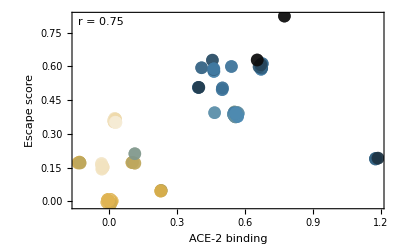

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,gaColors],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->gaPanel]
```

```mathematica
Export["figures/binding_escape_correlation_ramp.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation_ramp.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1 and binding X_2

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{x1,x2},{x1,x2}]
```

FittedModel[0.975043+0.603498 x1+1.08904 x2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.975043 | 0.030716 | 31.7438 | 5.07925×10^-65
x1 | 0.603498 | 0.135274 | 4.4613 | 0.0000168411
x2 | 1.08904 | 0.0934514 | 11.6536 | 3.09462×10^-22